```mathematica
(*Question 1*)
g =QuantityMagnitude[UnitConvert[Quantity[1,"StandardAccelerationOfGravity"]]];
DistanceTheta[v0_,θ_]:=DSolve[{x''[t],y''[t],x[0],y[0],x'[0],y'[0]}=={0,-g,0,0,v0*Cos[θ Degree],v0*Sin[θ Degree]},{x[t],y[t]},t]
xx = x[t]/.DistanceTheta[v,θ][[1]]/.t->t/.Solve[{y[t]==0/.DistanceTheta[v,θ][[1]],t!=0},t][[1]];
Solve[D[xx,θ]==0,θ]
```

{{θ→ConditionalExpression[(-(3 π)/4+2 π C[1])/°,C[1]∈ℤ]},{θ→ConditionalExpression[(-π/4+2 π C[1])/°,C[1]∈ℤ]},{θ→ConditionalExpression[(π/4+2 π C[1])/°,C[1]∈ℤ]},{θ→ConditionalExpression[((3 π)/4+2 π C[1])/°,C[1]∈ℤ]}}

```mathematica
(*Question 2*)
(*General Form*)
Distance[x0_,y0_,xv0_,yv0_]:= DSolve[{x''[t],y''[t],x[0],y[0],x'[0],y'[0]}=={0,-g,x0,y0,xv0,yv0},{x[t],y[t]},t]
NDistance[x0_,y0_,xv0_,yv0_]:= NDSolve[{x''[t],y''[t],x[0],y[0],x'[0],y'[0]}=={0,-g,x0,y0,xv0,yv0},{x[t],y[t]},{t,0,1000}]
```

```mathematica
(*Plots for Values of θ*)
```

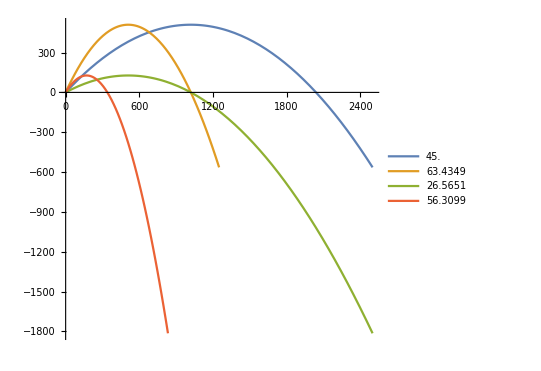

```mathematica
n=100;
Dist1 =Evaluate[{x[t],y[t]}/.NDistance[0,0,n,n]];
Dist2 =Evaluate[{x[t],y[t]}/.NDistance[0,0,n/2,n]];
Dist3 = Evaluate[{x[t],y[t]}/.NDistance[0,0,n,n/2]];
Dist4 = Evaluate[{x[t],y[t]}/.NDistance[0,0,n/3,n/2]];
ParametricPlot[{Dist1,Dist2,Dist3,Dist4},{t,0,25},PlotLegends->{N[ArcTan[n/n]/°],N[ArcTan[n/(n/2)]/°],N[ArcTan[(n/2)/n]/°],N[ArcTan[(n/2)/(n/3)]/°]}]
```

```mathematica
(*Rewritten to just take inputs for V0 and θ*)
```

```mathematica
NDistanceTheta[v0_,θ_]:=NDSolve[{x''[t],y''[t],x[0],y[0],x'[0],y'[0]}=={0,-g,0,0,v0*Cos[θ Degree],v0*Sin[θ Degree]},{x[t],y[t]},{t,0,1000}]
```

```mathematica
DistTh1 =Evaluate[{x[t],y[t]}/.NDistanceTheta[100,45]];
DistTh2 =Evaluate[{x[t],y[t]}/.NDistanceTheta[100,30]];
DistTh3 =Evaluate[{x[t],y[t]}/.NDistanceTheta[100,60]];
DistTh4 =Evaluate[{x[t],y[t]}/.NDistanceTheta[100,90]];
```

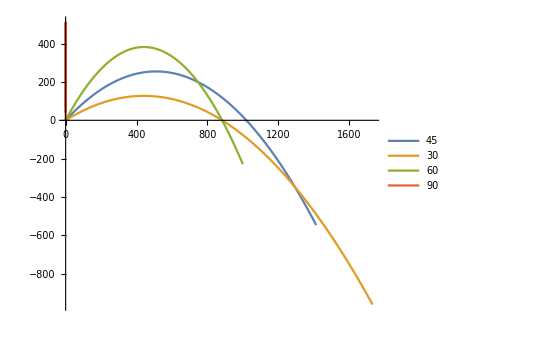

-Graphics-

```mathematica
ParametricPlot[{DistTh1,DistTh2,DistTh3,DistTh4},{t,0,20},PlotLegends->{45,30,60,90}]
```

```mathematica
(*You can manipulate θ and see its effect*)
```

```mathematica
Manipulate[ParametricPlot[Evaluate[{x[t],y[t]}/.NDistanceTheta[100,θ]],{t,0,100},PlotRange->{{0,1100},{0,500}}],{θ,0,90}]
```

```mathematica
(*Question 3*)
```

```mathematica
ρ = QuantityMagnitude[StandardAtmosphereData[Quantity[0,"Feet"],"Density"]]; (*kg/m^3*)
r = 0.05 (*Meters*);
m = 0.5 (*Kilograms*);
A = r^2/2;
T = 1000;
DistanceThetaDrag[v0_,θ_]:=DSolve[{x''[t],y''[t],x[0],y[0],x'[0],y'[0]}=={(Abs[-ρ A ]/m)(-x'[t]*Sqrt[(x'[t]^2+y'[t]^2)]),-g-(Abs[-ρ A ]/m)(y'[t]*Sqrt[(x'[t]^2+y'[t]^2)]),0,0,v0*Cos[θ Degree],v0*Sin[θ Degree]},{x[t],y[t]},t]
NDistanceThetaDrag[v0_?NumericQ,θ_?NumericQ]:=NDSolve[{x''[t],y''[t],x[0],y[0],x'[0],y'[0]}=={(Abs[ρ A ]/m)(-x'[t]*Sqrt[(x'[t]^2+y'[t]^2)]),-g-(Abs[ρ A ]/m)(y'[t]*Sqrt[(x'[t]^2+y'[t]^2)]),0,0,v0*Cos[θ Degree],v0*Sin[θ Degree]},{x[t],y[t]},{t,0,T}]
```

```mathematica
(*Plot of trajectory with drag*)
```

```mathematica
Manipulate[ParametricPlot[Evaluate[{x[t],y[t]}/.NDistanceThetaDrag[1000,θ]],{t,0,100},PlotRange->{{0,1200},{0,1000}}],{θ,0,90}]
```

```mathematica
(*Optimization*)
```

```mathematica
(*Without Drag*)
```

```mathematica
Time[v0_,θ_]:=t/.FindRoot[y[t]/.NDistanceTheta[v0,θ],{t,1000}];
xmax [v0_,θ_]:= (x[t]/.NDistanceTheta[v0,θ]/.t->Time[v0,θ])[[1]]
DistanceFind = xmax[100,45];
```

```mathematica
(*With Drag*)
```

```mathematica
(*We shouldn't have a lower velocity in the drag case be able to go as far as the one we started with ignoring drag*)
```

```mathematica
TimeDrag[v0_?NumericQ,θ_?NumericQ]:= t/.FindRoot[y[t]/.NDistanceThetaDrag[v0,θ],{t,T}]
xmaxDrag[v0_?NumericQ,θ_?NumericQ]:= (x[t]/.NDistanceThetaDrag[v0,θ]/.t->TimeDrag[v0,θ])[[1]]
VelocityFinder[θ_?NumericQ,tolerance_?NumericQ]:=Module[{v0},
v0=0.0001;
While[Abs[xmaxDrag[v0,θ]-DistanceFind]>250,v0;v0=v0+100];
While[Abs[xmaxDrag[v0,θ]-DistanceFind]>100,v0;v0=v0+50];
While[Abs[xmaxDrag[v0,θ]-DistanceFind]>10,v0;v0=v0+5];
While[Abs[xmaxDrag[v0,θ]-DistanceFind]>tolerance,v0;v0=v0+tolerance/10];
v0
]
ThetaFinderHigh[v0_?NumericQ,tolerance_]:=Module[{θ},
θ  = 90;
While[Abs[xmaxDrag[v0,θ]-DistanceFind]>20 &&θ>0,θ; θ=θ-1];
While[Abs[xmaxDrag[v0,θ]-DistanceFind]>1 &&θ>0,θ; θ=θ-(tolerance/10)];
θ
]
ThetaFinderLow[v0_?NumericQ,tolerance_]:=Module[{θ},
θ  = 0;
While[Abs[xmaxDrag[v0,θ]-DistanceFind]>20 &&θ < 90,θ; θ=θ+1];
While[Abs[xmaxDrag[v0,θ]-DistanceFind]>1 &&θ<90,θ; θ=θ+(tolerance/10)];
θ
]
OptimizeVelocity[vTolerance_,θlow_,θhigh_,θStep_]:=Module[{θ,t,v,v1},
v1=1000000;t=0;
For[θ=θlow,θ≤θhigh,θ= θ+θStep,
v =VelocityFinder[θ,vTolerance];
If[v<v1,{v1=v,t=θ},{v1=v1,t=t}]
];
{v1,t}
]
```

```mathematica
(*The Two θs for a initial velocity higher than the Drag-free case, should be complimentary, θ1+θ2=90*)
```

```mathematica
OptimizeVelocity[1,10,55,1]
{vop,θop}=OptimizeVelocity[1,20,26,0.1]
```

{698.7,24}

{698.7,23.8}

```mathematica
DistTh1Drag ={x[t],y[t]}/.NDistanceThetaDrag[vop,θop];
DistTh2Drag ={x[t],y[t]}/.NDistanceThetaDrag[VelocityFinder[45,1],45];DistTh3Drag ={x[t],y[t]}/.NDistanceThetaDrag[VelocityFinder[60,1],60];
DistTh4Drag ={x[t],y[t]}/.NDistanceThetaDrag[VelocityFinder[20,1],20];
```

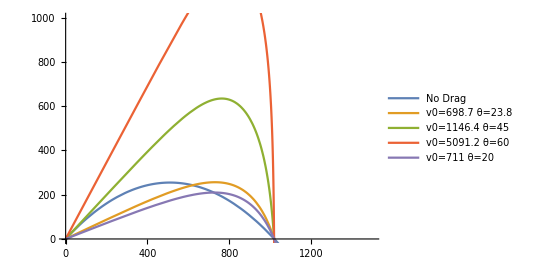

```mathematica
ParametricPlot[{DistTh1,DistTh1Drag,DistTh2Drag,DistTh3Drag,DistTh4Drag},{t,0,100},PlotLegends->{"No Drag","v0=698.7 θ=23.8","v0=1146.4 θ=45","v0=5091.2 θ=60","v0=711 θ=20"},PlotRange->{{0,1500},{0,1000}}]
```